# Gravity Tunnel inside the Earth with and effective density function.

## Densities definition

#### Effective density functions

First, we define the value of the constants that we are going to use: Acceleration of gravity, radius of the Earth and mean density of the Earth:

```mathematica
g=9.8156;  (*m/s2*)  
R=6.371 10^3; (*km*)          
ρ 0 = 5515 ; (*kg/m3*)
```

Now, after the determination of the first parameter ‘a’  by integration and equating to the mass of the Earth, we get the following weight functions

```mathematica
k1[b_]:=Sum[QBinomial [b,n,1](-1)^n/(n+3) ,{n,0,10}];
(*k2[b_,c_]:= ∑_(n=0)^10 QBinomial[b,n,1](-c)^n/(n+3);*)
k2[b_,c_]:=Sum[QBinomial[b,n,1] (-1-c)^n NIntegrate[x^(n+2)/(1+c x)^n,{x,0,1}] ,{n,0,10}]
(*  ∑_(n=0)^10 QBinomial[b,n,1] (-1-c)^n ∫_0^1 x^(n+2)/(1+c x)^n ⅆx *)
```

with this, the densities can be written

```mathematica
ρ1[r_,b_]:=(ρ 0)/(3 k1[b]) (1-r/R)^b;  
ρ2[r_,b_,c_]:=(ρ 0)/(3 k2[b,c])  (1 - ((1+c)r/R)/(1+c r/R))^b;
(*ρ2[r_,b_,c_]:=(ρ 0)/(3 k2[b,c]) (1-c r/R)^b  ;*)
```

we can now plot them

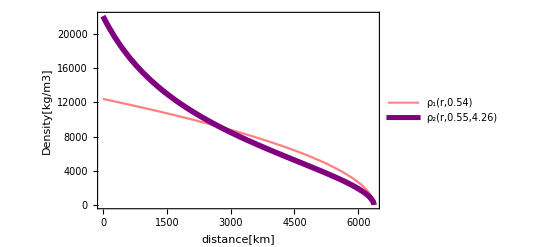

```mathematica
Functions=Plot[{ρ1[x,0.5418],ρ2[x,0.55,4.26]},{x,0,R},
PlotLegends->Placed[{"ρ_1(r,0.54)","ρ_2(r,0.55,4.26)"},{Right,Top}],
PlotStyle->{{Thickness[0.004],Pink},{Purple,Thickness[0.01]}},
Frame->True,
FrameLabel->{{"Density[kg/m3]",None},{"distance[km]",None}}]
```

#### Numerical density from PREM

Now, let’s import PREM data and plot to see how this distribution looks like

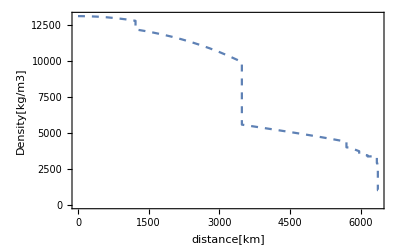

```mathematica
density prem=Import["/home/nicolas/Documents/Trabajo de Grado/Numerical Data/prem-density.csv","Table"];
data=ListLinePlot[density prem,
PlotStyle->Dashed,
Frame->True,
FrameLabel->{{"Density[kg/m3]",None},{"distance[km]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Trabajo de Grado/Plots/density_prem.pdf",density prem];
```

To compare, we can plot them together

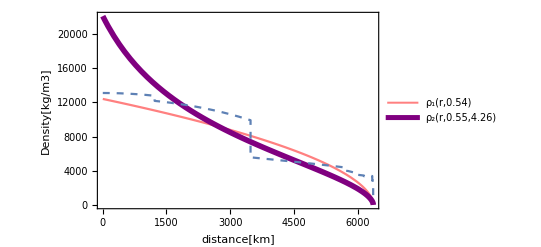

```mathematica
densities = Show[Functions,data]
```

we see that actually the proposed functions fit between the data.

```mathematica
Export["/home/nicolas/Documents/Trabajo de Grado/Plots/densities.pdf",densities];
```

### Masses

Now, we want to determine the mass as a function of the radius. Ar r=R we would like to have M(r) = M ~ 6 x 10^15,

```mathematica
M1[r_,b_]:= 4 π  NIntegrate[ρ1[x,b] x^2 ⅆx,{x,0,r}]
M2[r_,b_,c_]:= 4 π  NIntegrate[ρ2[x,b,c]x^2,{x,0,r}]
(*∫_0^r ρ3[x,b,c] x^2 ⅆx*)
```

the output at the radius is

```mathematica
{M1[R,0.54],M2[R,0.55,4.26]}
```

{5.8025×10^15,5.03203×10^15}

the expected one.  To see the behaviour at any other point let’s plot this functions

```mathematica
Plot[{M1[r,0.7],M2[r,0.54,0.04]},{r,0,R},
PlotLegends->Placed[{"ρ_1(r,0.54)","ρ_2(r,0.55,4.26)"},{Right,Top}],
PlotStyle->{{Thickness[0.004],Pink},{Purple,Thickness[0.01]}},
Frame->True,
FrameLabel->{{"Density[kg]",None},{"distance[km]",None}}]
```

-Graphics-

### Gravity

#### From density functions

```mathematica
a1[r_,b_]:=g/k1[b] ∑_(k=0)^10 QBinomial[b,k,1] (-1)^k/(k+3) (r/R)^(k+1) ;
a2[r_,b_,c_]:=  g/k2[b,c] R/r^2 Sum[ QBinomial[b,n,1](-1-c)^n NIntegrate[(x/R)^(n+2)/(1+c x/R)^n,{x,0,r}],{n,0,10}]
(*a2[r_,b_,c_]:=g/k2[b,c] * Sum[QBinomial[b,k,1]*(-c)^k R^(-k-1) r^(k+1) /(k+3),{k,0,10}];*)
```

at the surface we have

```mathematica
{a1[R,0.54],a2[R,0.5,0.04]}
```

{9.8156,9.8156}

as it should be.

#### From Prem

Here we write the official data in the pertinent units and in interpolate it to have a continuous function

```mathematica
gravity prem = Import["/home/nicolas/Documents/Trabajo de Grado/Numerical Data/gravity_prem.csv","Table"];
g prem=Interpolation[gravity prem,InterpolationOrder->5]
```

InterpolatingFunction[…]

Now, we can plot the three functions together

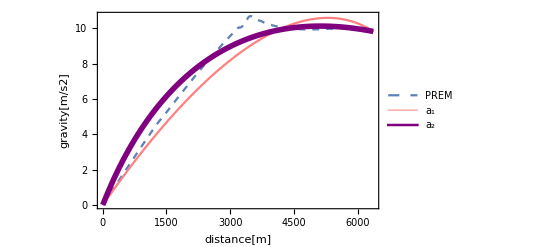

```mathematica
accelerations = Plot[{g prem[r],a1[r,0.5418],a2[r,0.55,4.26]},{r,0,R},
PlotLegends->Placed[{"PREM","a_1","a_2"},{Right,Bottom}],
PlotStyle->{Dashed,{Thickness[0.004],Pink},{Purple,Thickness[0.01]}},
Frame->True,
FrameLabel->{{"gravity[m/s2]",None},{"distance[m]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Trabajo de Grado/Plots/accelerations.pdf",accelerations];
```

## Velocity Profiles

Next, we are going to compute the velocities of the already found density profiles,

```mathematica
vprem[r_?NumberQ] := Sqrt[2*NIntegrate[ g prem[x], {x, r, R}]]
v1[r_,b_]:=Sqrt[2g/(k1[b]) Sum[QBinomial[b,k,1]*(-1)^k R^(-k-1) (R^(k+2) - r^(k+2))/((k+2)(k+3)),{k,0,10}]]
v2[r_,b_,c_]:=Sqrt[2g/(k2[b,c]) Sum[QBinomial[b,k,1]*(-1-c)^k NIntegrate[(x/R)^(k+2)/(1+c x/R)^k R/y^2,{y,r,R},{x,0,y}],{k,0,10}]]
(*v2[r_,b_,c_]:=Sqrt[2g/(k2[b,c]) *Sum[QBinomial[b,k,1]*(-c)^k R^(-k-1) (R^(k+2) - r^(k+2))/((k+2)(k+3)),{k,0,10}]]*)
```

we can here take some arbitrary values to have an idea of the closeness of the two functions and the expected value given by PREM

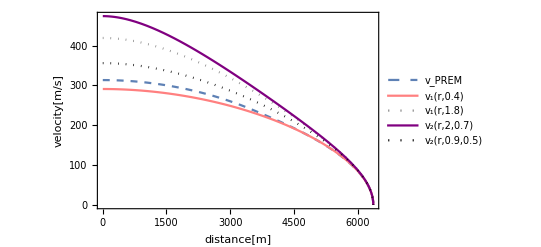

```mathematica
somevelocities = Plot[{vprem[x],v1[x,0.4 ],v1[x,1.8],v2[x,2,0.7],v2[x,0.9,0.5]},{x,0,R},
PlotLegends->Placed[{"v_PREM","v_1(r,0.4)","v_1(r,1.8)","v_2(r,2,0.7)","v_2(r,0.9,0.5)"},{Left,Bottom}],
PlotStyle->{Dashed,Pink,{Dotted,Gray},Purple,{Dotted,Black}},
Frame->True,
FrameLabel->{{"velocity[km/s]",None},{"distance[m]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Trabajo de Grado/Plots/some-velocities.pdf",somevelocities];
```

For the optimum value found in the next section, we can compare the values for this velocities when the train is passing through the center of the Earth

```mathematica
{vprem[0],v1[0,0.5418],v2[0,0.55,4.26]}
```

{313.531,306.33,316.404}

but the best way to compare is with a plot

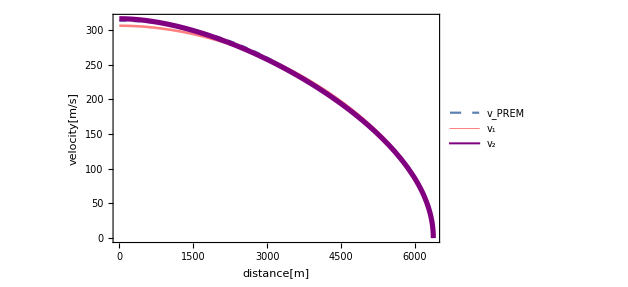

```mathematica
velocities = Plot[{vprem[x],v1[x,0.5418],v2[x,0.55,4.26]},{x,0,R},
PlotLegends->Placed[{"v_PREM","v_1","v_2"},{Right,Top}],
PlotStyle->{Dashed,{Thickness[0.004],Pink},{Purple,Thickness[0.008]}},
Frame->True,
FrameLabel->{{"velocity[m/s]",None},{"distance[m]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Trabajo de Grado/Plots/velocities.pdf",velocities];
```

let’s zoom in on a particular region

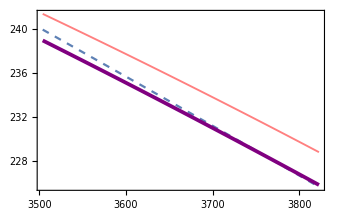

```mathematica
Plot[{vprem[x],v1[x,0.5418],v3[x,0.55,4.26]},{x,0.55 R,0.6 R},
PlotStyle->{Dashed,{Thickness[0.004],Pink},{Purple,Thickness[0.008]}},
Frame->True,
FrameTicks->None]
```

## Minimization

Now, let’s find the best parameters for the description of the Earth’s interior, first, redefine the non-dimensional gravity profile

```mathematica
gravity prem ad=Import["/home/nicolas/Documents/Trabajo de Grado/Numerical Data/prem-grav-ad.csv","Table"];
g prem ad=Interpolation[gravity prem ad];
```

with this we define the non-dimensional velocity

```mathematica
vprem ad[r_?NumberQ] := Sqrt[2*NIntegrate[ g prem ad[x], {x, r, 1}]]
```

Now define the non-dimensional version of the velocities

```mathematica
v1 ad[r_,b_]:=Sqrt[2/(k1[b]) *Sum[QBinomial[b,k,1]*(-1)^k  (1 - r^(k+2))/((k+2)(k+3)),{k,0,10}]]
v2 ad[r_?NumberQ,b_,c_]:=Sqrt[2/(k2[b,c]) Sum[QBinomial[b,k,1]*(-1-c)^k NIntegrate[x^(k+2)/(1+c x)^k 1/y^2,{y,r,1},{x,0,y}],{k,0,10}]]
(*v2 ad[r_,b_,c_]:=Sqrt[2/(k2[b,c]) *Sum[QBinomial[b,k,1]*(-c)^k  (1 - r^(k+2))/((k+2)(k+3)),{k,0,10}]]*)
```

They are all put into the functions to minimize, and can be directly minimized (can take a while)

```mathematica
f1[b_?NumericQ]:=NIntegrate[(1/v1 ad[r,b] - 1/vprem ad[r] )^2,{r,0,1},Method->"LocalAdaptive"];NMinimize[f1[b],{b},Method -> "NelderMead"]
```

{0.000425219,{b→0.541844}}

```mathematica
f2[b_?NumericQ,c_?NumericQ]:=NIntegrate[(1/v2 ad[r,b,c] - 1/vprem ad[r] )^2,{r,0,1},Method->"LocalAdaptive"];
NMinimize[f2[b,c],{b,c},Method -> "NelderMead"]
```

{0.0000253253,{b→9.13735,c→0.179943}}

```mathematica
f3[b_?NumericQ,c_?NumericQ]:=NIntegrate[(1/v3 ad[r,b,c] - 1/vprem ad[r] )^2,{r,0,1},Method->"LocalAdaptive"];
NMinimize[f3[b,c],{b,c},Method -> "NelderMead"]
```

## Times chord path

We have arrived to the most important part of this work, the traversal time of the train.

```mathematica
T prem[d_]:= NIntegrate[x/(vprem ad[x]*Sqrt[x^2 - d^2 ]),{x,d,1}]
T1[d_]:= NIntegrate[x/(v1 ad[x,0.5418]*Sqrt[x^2 - d^2 ]),{x,d,1}]
T2[d_]:= NIntegrate[x/(v2 ad[x,9.131774,0.179936]*Sqrt[x^2 - d^2 ]),{x,d,1}]
T3[d_]:= NIntegrate[x/(v3 ad[x,0.55,4.26]*Sqrt[x^2 - d^2 ]),{x,d,1}]
```

given the functions, we should check that the values for the tunnel across the center of the Earth are in some way close

```mathematica
{T prem[0],T1[0],T3[0]}
```

{1.42206,1.4186,1.42268}

this means an error of

```mathematica
{(T prem[0]-T1[0])/(T prem[0])*100,(T3[0]-T prem[0])/(T prem[0])*100}
```

{0.243384,0.0435752}

But, again, the best way to compare the results is with a plot

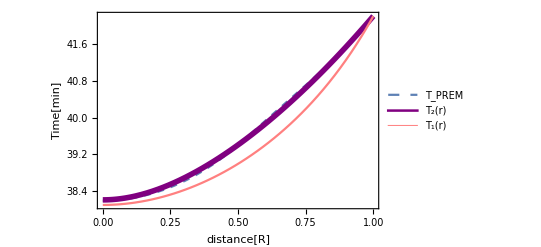

```mathematica
chordtimes = Plot[{T prem[x]*26.86259993217512, T3[x]*26.86259993217512,T1[x]*26.86259993217512},{ x,0,1},
PlotLegends->Placed[{"T_PREM","T_2(r)","T_1(r)"},{Left,Top}],
PlotStyle->{Dashed,{Purple,Thickness[0.01]},{Thickness[0.004],Pink}},
Frame->True,
FrameLabel->{{"Time[min]",None},{"distance[R]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Trabajo de Grado/Plots/times.pdf",chordtimes];
```

## Brachistochrone

### Shape of the brachistochrone curves

The other important part of this work is the time for the path of fastest descent and its shape. To find it we need first to define auxiliary functions for the integration,

```mathematica
I1[x_,d_]:=1/(Sqrt[x^4/(d)^2 *(v1 ad[d,0.5418]/v1 ad[x,0.5418])^2-x^2] )
I2[x_,d_]:=1/(Sqrt[x^4/(d)^2 *(v2 ad[d,0.55,4.26]/v2 ad[x,0.55,4.26])^2-x^2] )
I prem[x_,d_]:=1/(Sqrt[x^4/d^2 *(vprem ad[d]/vprem ad[x])^2-x^2] )
```

Now we can proceed to do the integration in a valid range

```mathematica
θ1 [r_?NumericQ,d_?NumericQ]:=If[r>d,NIntegrate[I1[x,d],{x,d,r}],0.0]
θ2 [r_?NumericQ,d_?NumericQ]:=If[r>d,NIntegrate[I2[x,d],{x,d,r}],0.0]
θ prem [r_?NumericQ,d_?NumericQ]:=If[r>d,NIntegrate[I prem[x,d],{x,d,r}],0.0]
```

In order to plot this in an appropriate way (maybe there is a better way), we need to extract some values

```mathematica
{FindRoot[θ1[1,d]- Pi/3,{d,0.1},AccuracyGoal->4,PrecisionGoal->4],
FindRoot[θ1[1,d]-Pi/6,{d,0.6},AccuracyGoal->4,PrecisionGoal->4]}
{FindRoot[θ2[1,d]-Pi/3,{d,0.1},AccuracyGoal->4,PrecisionGoal->4], 
FindRoot[θ2[1,d]-Pi/6,{d,0.6},AccuracyGoal->4,PrecisionGoal->4]}
{FindRoot[θ prem[1,d]-Pi/3,{d,0.1},AccuracyGoal->4,PrecisionGoal->4],FindRoot[θ prem[1,d]-Pi/6,{d,0.6},AccuracyGoal->4,PrecisionGoal->4]}
```

{{d→0.310287},{d→0.647024}}

{{d→0.298391},{d→0.63938}}

{{d→0.301061},{d→0.643903}}

```mathematica
braq13=Table[{θ1[i,0.310],i},{i,0.310,1,0.001}];
braq23=Table[{θ2[i,0.2984],i},{i,0.2984,1,0.001}];
braq16=Table[{θ1[i,0.647],i},{i,0.65,1,0.01}];
braq26=Table[{Re[θ2[i,0.639]],i},{i,0.640,1,0.001}];
braq prem3=Table[{θ prem[i,0.301],i},{i,0.301,1,0.001}];
braq prem6=Table[{Re[θ prem[i,0.6439]],i},{i,0.6439,1,0.001}];
```

Here we export them to plot the graphs more easily in gnuplot.

```mathematica
Export["braq13.csv",braq13,"Table"]
Export["braq16.csv",braq16,"Table"]
Export["braq23.csv",braq23,"Table"]
Export["braq26.csv",braq26,"Table"]
Export["braqprem3.csv",braq prem3,"Table"]
Export["braqprem6.csv",braq prem6,"Table"]
```

### Times for the brachistochrone curves

In this subsection we are going to find the times found for the brachistochrone paths. As this are by definition the paths of fastest descent, the times should be the minimal times. To do this we need the derivative of the trajectory

```mathematica
ω1[r_, d_]=Re[D[θ1[x,d],x]/. x->r];
ω2[r_, d_]=D[θ2[x,d],x]/. x->r;
ω prem[r_, d_]=D[θ prem[x,d],x]/. x->r;
```

and  then the times for a given maximum approaching point d

```mathematica
Tbraq1[d_?NumericQ]:=NIntegrate[Sqrt[1+r^2 ω1[r,d]^2]/v1 ad[r,0.5418],{r,d,1}]
Tbraq2[d_?NumericQ]:=NIntegrate[Sqrt[1+r^2 ω2[r,d]^2]/v3 ad[r,0.55,4.26],{r,d,1}]
Tbraq prem[d_?NumericQ]:=NIntegrate[Sqrt[1+r^2 ω prem[r,d]^2]/vprem ad[r],{r,d,1}]
```

let’s check that the times taken when d=0 are the same as for the chord path

```mathematica
{Tbraq prem[0.],Tbraq2[0.],Tbraq1[0.]}
```

{1.42206,1.42268,1.4186}

they are almost the same, maybe it’s a question of precision, but we can trust in this results. We can see the complete dependence of the times on the position of the tunnel in the following plot

```mathematica
Plot[{Tbraq prem[x], Tbraq2[x],Tbraq1[x]},{ x,0,1},
PlotLegends->Placed[{"t_PREM","t_2(r)","t_1(r)"},{Left,Bottom}],
PlotStyle->{Dashed,Purple,Pink},
Frame->True,
FrameLabel->{{"Time[min]",None},{"distance[R]",None}}]
```

$Aborted

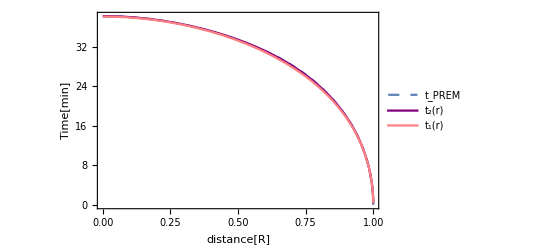

```mathematica
braqtimes=Plot[{Tbraq prem[x]*26.86259993217512, Tbraq2[x]*26.86259993217512,Tbraq1[x]*26.86259993217512},{ x,0,1},
PlotLegends->Placed[{"t_PREM","t_2(r)","t_1(r)"},{Left,Bottom}],
PlotStyle->{Dashed,Purple,Pink},
Frame->True,
FrameLabel->{{"Time[min]",None},{"distance[R]",None}}]
```

```mathematica
Export["/home/nicolas/Documents/Trabajo de Grado/Plots/braqtimes.pdf",braqtimes];
```

## Accelerations

In this last section, we want give a dynamical reason for the difference between chord path times and brachistochrone path times. First, define some auxiliary functions

```mathematica
dist1[d_]:=Sqrt[1-(Sin[θ1[1,d]])^2]
dist2[d_]:=Sqrt[1-(Sin[θ2[1,d]])^2]
dist prem[d_]:=Sqrt[1-(Sin[θ prem[1,d]])^2]
```

Now we compute the radial accelerations

```mathematica
arad1[r_]:=1/k1[0.5418] * Sum[QBinomial[0.5418,k,1]*(-1)^k  r^(k+1)/(k+3),{k,0,10}];
arad2[r_]:=1/k2[0.55,4.26] * Sum[QBinomial[0.55,k,1]*(-1-4.26)^k  NIntegrate[(x)^(k+2)/(1+4.26 x)^k,{x,0,r}],{k,0,10}]/r^2;
arad prem=g prem ad;
```

with these and the auxiliary functions y can define the acceleration in the direction of motion for the chord path

```mathematica
a1[x_,d_]:=arad1[x]*Sqrt[x^2-(dist1[d])^2]/x
a2[x_,d_]:=arad2[x]*Sqrt[x^2-(dist2[d])^2]/x
a prem[x_,d_]:=arad prem[x]*Sqrt[x^2-(dist prem[d])^2]/x
```

as well as the acceleration in the direction of motion for the brachistochrone paths

```mathematica
abraq1[x_,d_]:=arad1[x]*Sin[θ1 [x, d]]
abraq2[x_,d_]:=arad2[x]*Sin[θ2 [x, d]]
abraq prem[x_,d_]:=arad prem[x]*Sin[θ prem[x, d]]
```

```mathematica
Table[abraq1[x,0.2],{x,0.3,1,0.01}]
```

{0.425022,0.447787,0.4697,0.490853,0.511316,0.531148,0.550396,0.5691,0.587291,0.604998,0.622242,0.639044,0.65542,0.671383,0.686947,0.702122,0.716915,0.731336,0.745389,0.759081,0.772415,0.785396,0.798026,0.810308,0.822244,0.833834,0.845079,0.85598,0.866536,0.876747,0.886612,0.89613,0.905298,0.914115,0.922578,0.930686,0.938434,0.945819,0.952838,0.959488,0.965762,0.971658,0.97717,0.982292,0.98702,0.991347,0.995266,0.998772,1.00186,1.00451,1.00673,1.00851,1.00983,1.01068,1.01107,1.01097,1.01037,1.00927,1.00765,1.0055,1.00281,0.999551,0.995722,0.991302,0.986275,0.980622,0.974326,0.967364,0.959715,0.951354,0.942244}

Now, let’s plot

```mathematica
accelerations1 =Plot[{Table[9.81*a2[x,d],{d,0.1,0.5,0.2}],Table[9.81*abraq1[x,d],{d,0.1,0.5,0.2}]},{x,0,1},
PlotRange->{0.0001,10.6},
PlotLegends->Placed[{"a_CHORD","a_BRAQ"},{Left,Top}],
PlotStyle->{Pink,Purple},
Frame->True,
FrameLabel->{{"acceleration[m/s2]",None},{"distance[R]",None}}]
```

$Aborted

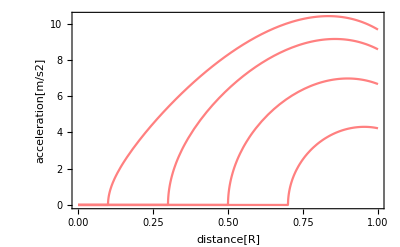

```mathematica
accelerations2 = Plot[Table[9.81*abraq1[x,d],{d,0.1,0.8,0.2}],{x,0,1},
PlotStyle->{Pink},
Frame->True,
FrameLabel->{{"acceleration[m/s2]",None},{"distance[R]",None}}]
```

```mathematica
a1 d01=Table[{x,9.81*abraq1[x,0.1]},{x,0.11,1,0.001}]
a1 d03=Table[{x,9.81*abraq1[x,0.3]},{x,0.11,1,0.001}];
a1 d05=Table[{x,9.81*abraq1[x,0.5]},{x,0.11,1,0.001}];
```

```mathematica
Export["/home/nicolas/Documents/Trabajo de Grado/Numerical Data/achord1d01.csv",a1 d01,"Table"];
Export["/home/nicolas/Documents/Trabajo de Grado/Numerical Data/achord1d03.csv",a1 d03,"Table"];
Export["/home/nicolas/Documents/Trabajo de Grado/Numerical Data/achord1d05.csv",a1 d05,"Table"];
```